```mathematica
(*example discrete rwd data for time-dependent decreasing task*)
data={{0.5,10},{1,5},{2,3},{4,2},{5,1},{6,0.5}};
```

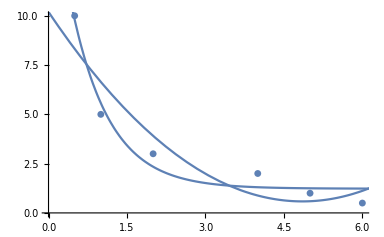

```mathematica
(*2 fitting funcs for data*)
Show[ListPlot[data],Plot[Exp[-1.361x+2.829]+1.23,{x,-1,10}],Plot[10.198-3.961 x+0.408 x^2,{x,0,10}]]
```

```mathematica
FindFit[data, Exp[a x+b]+c,{a,b,c},x]
```

{a→-1.36157,b→2.8293,c→1.22999}

```mathematica
FindFit[data, a+b x+c x^2,{a,b,c},x]
```

{a→10.198,b→-3.96126,c→0.408452}

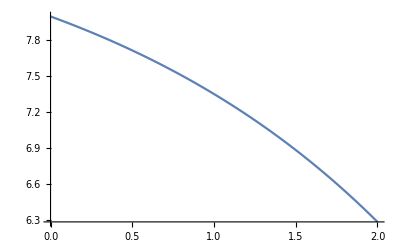

```mathematica
(*example of rwd func of fixed-ddl tasks, concave func*)
Plot[10-(1*Exp[0.5*x]+1),{x,0,2}]
```

```mathematica
(*find fitting rwd func for asap task*)
app=10;rwd=5;
data={{0,rwd},{app*1.4,rwd/2},{app*2.5,rwd/5}};
FindFit[data, a Exp[-b x]+rwd-a,{a,b,c},x]
```

General::munfl: -11.25/(-7.98120765338625×10^2798008) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

{a→3.25,b→14193.5,c→1.}

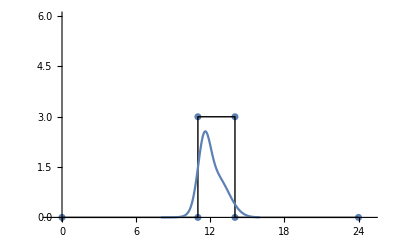

```mathematica
(*rwd func for meal*)
rwd=3;
data={{0,0},{11,0},{11,rwd},{14,rwd},{14,0},{24,0}};
Show[ListPlot[data,PlotRange->{{-1,25},{0,6}}],Graphics[Line[data]],Plot[0.6*rwd*Exp[-(x-11.5)^2/(2*0.5^2)]+0.4*rwd*Exp[-(x-12.5)^2/(2*1^2)],{x,8,16}]]
```

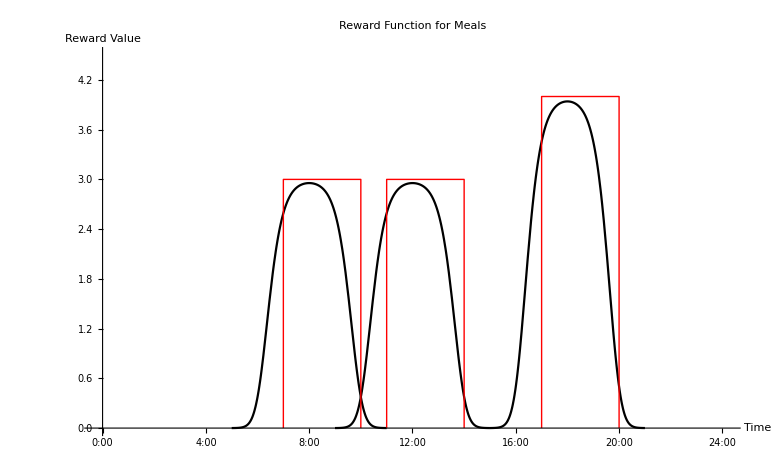

```mathematica
(*new rwd func for meal: generalised logistic func*)
(*logistic contribution: y=1/(1+e^(-(x-u)/b))^a*)
(*logistic sigmoid: y=1/(1+e^-x)*)
meal[x_,l_,r_, rwd_]:=rwd*LogisticSigmoid[(x-l+1)*3]^3+rwd*LogisticSigmoid[(r-x)*3]^3-rwd
data={{0,0},{early,0},{early,rwd},{late,rwd},{late,0},{24,0}};
Show[Plot[meal[x,7,10,3],{x,5,11}, PlotStyle->Black],Plot[meal[x,11,14,3],{x,9,15}, PlotStyle->Black],Plot[meal[x,17,20,4],{x,15,21}, PlotStyle->Black],Graphics[{Red,Line[{{7,0},{7,3},{10,3},{10,0}}]}],Graphics[{Red,Line[{{11,0},{11,3},{14,3},{14,0}}]}],Graphics[{Red,Line[{{17,0},{17,4},{20,4},{20,0}}]}],  PlotRange->{{-0.2,24.2},{0,4.5}},AxesOrigin->{0,0},AxesStyle->{{Directive[Black, 12],Arrowheads[0.015]},{Directive[Black, 12],Arrowheads[0.015]}}, PlotLabel->"Reward Function for Meals",AxesLabel->{"Time", "Reward Value"},Ticks->{{{0,"0:00"},{4,"4:00"},{8,"8:00"},{12,"12:00"},{16,"16:00"},{20,"20:00"},{24,"24:00"}},Automatic},  LabelStyle->Directive[Black,13,Thick]]
```

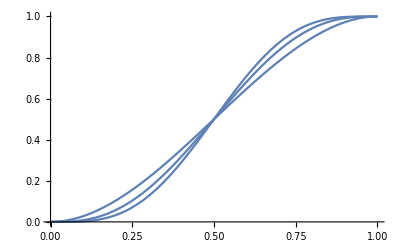

```mathematica
(*smoothstep func*)
Show[Plot[-2 x^3+3 x^2,{x,0,1}],Plot[6 x^5-15 x^4+10 x^3,{x, 0, 1}], Plot[-20 x^7+70 x^6-84 x^5+35 x^4,{x,0,1}]]
```

```mathematica
(*rwd func for sleeping*)
dur[x_, durMin_, durMax_, rwd_]:=Piecewise[{{rwd*(1-Exp[-0.8(x-durMin)]),durMin≤x≤durMax},{0,x<durMin},{0,x>durMax}}];
bed[x_,bedMin_,bedMax_,rwd_]:=Piecewise[{{rwd*Exp[-x+bedMin],bedMin≤x≤24},{rwd*Exp[-x-24+bedMin],0≤x≤bedMax},{0,bedMax≤x≤bedMin}}];
sleep[durx_,bedx_]:=Sqrt[dur[durx,durMin,durMax,rwd]*bed[bedx,bedMin,bedMax, rwd]];
durMin=5;durMax=12;bedMin=22;bedMax=4;rwd=5;
Plot3D[sleep[durx,bedx],{durx,5,12},{bedx,0,24},AxesLabel->{"duration/h", "bedtime/:00"}];
```

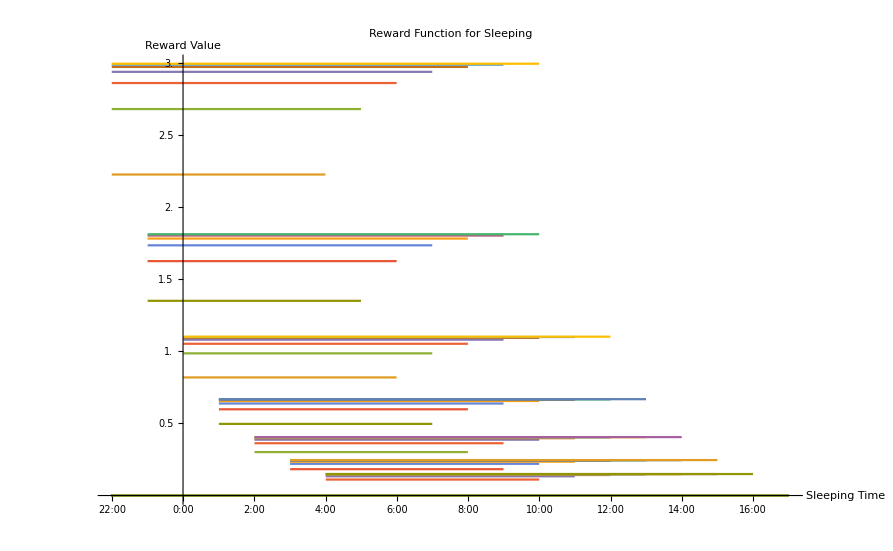

```mathematica
(*plot rwd func for sleeping*)
Plot[{Piecewise[{{sleep[5,22],-2≤x≤3}}],Piecewise[{{sleep[6,22],-2≤x≤4}}],Piecewise[{{sleep[7,22],-2≤x≤5}}],Piecewise[{{sleep[8,22],-2≤x≤6}}],Piecewise[{{sleep[9,22],-2≤x≤7}}],Piecewise[{{sleep[10,22],-2≤x≤8}}],Piecewise[{{sleep[11,22],-2≤x≤9}}],Piecewise[{{sleep[12,22],-2≤x≤10}}],Piecewise[{{sleep[5,23],-1≤x≤4}}],Piecewise[{{sleep[6,23],-1≤x≤5}}],Piecewise[{{sleep[7,23],-1≤x≤6}}],Piecewise[{{sleep[8,23],-1≤x≤7}}],Piecewise[{{sleep[9,23],-1≤x≤8}}],Piecewise[{{sleep[10,23],-1≤x≤9}}],Piecewise[{{sleep[11,23],-1≤x≤10}}],Piecewise[{{sleep[12,23],-1≤x≤11}}]Piecewise[{{sleep[5,0],0≤x≤5}}],Piecewise[{{sleep[6,0],0≤x≤6}}],Piecewise[{{sleep[7,0],0≤x≤7}}],Piecewise[{{sleep[8,0],0≤x≤8}}],Piecewise[{{sleep[9,0],0≤x≤9}}],Piecewise[{{sleep[10,0],0≤x≤10}}],Piecewise[{{sleep[11,0],0≤x≤11}}],Piecewise[{{sleep[12,0],0≤x≤12}}],Piecewise[{{sleep[5,1],1≤x≤6}}],Piecewise[{{sleep[6,1],1≤x≤7}}],Piecewise[{{sleep[7,1],1≤x≤8}}],Piecewise[{{sleep[8,1],1≤x≤9}}],Piecewise[{{sleep[9,1],1≤x≤10}}],Piecewise[{{sleep[10,1],1≤x≤11}}],Piecewise[{{sleep[11,1],1≤x≤12}}],Piecewise[{{sleep[12,1],1≤x≤13}}],Piecewise[{{sleep[5,2],2≤x≤7}}],Piecewise[{{sleep[6,2],2≤x≤8}}],Piecewise[{{sleep[7,2],2≤x≤9}}],Piecewise[{{sleep[8,2],2≤x≤10}}],Piecewise[{{sleep[9,2],2≤x≤11}}],Piecewise[{{sleep[10,2],2≤x≤12}}],Piecewise[{{sleep[11,2],2≤x≤13}}],Piecewise[{{sleep[12,2],2≤x≤14}}],Piecewise[{{sleep[5,3],3≤x≤8}}],Piecewise[{{sleep[6,3],3≤x≤9}}],Piecewise[{{sleep[7,3],3≤x≤10}}],Piecewise[{{sleep[8,3],3≤x≤11}}],Piecewise[{{sleep[9,3],3≤x≤12}}],Piecewise[{{sleep[10,3],3≤x≤13}}],Piecewise[{{sleep[11,3],3≤x≤14}}],Piecewise[{{sleep[12,3],3≤x≤15}}],Piecewise[{{sleep[5,4],4≤x≤9}}],Piecewise[{{sleep[6,4],4≤x≤10}}],Piecewise[{{sleep[7,4],4≤x≤11}}],Piecewise[{{sleep[8,4],4≤x≤12}}],Piecewise[{{sleep[9,4],4≤x≤13}}],Piecewise[{{sleep[10,4],4≤x≤14}}],Piecewise[{{sleep[11,4],4≤x≤15}}],Piecewise[{{sleep[12,4],4≤x≤16}}],Piecewise[{{sleep[5,5],5≤x≤10}}],Piecewise[{{sleep[6,5],5≤x≤11}}],Piecewise[{{sleep[7,5],5≤x≤12}}],Piecewise[{{sleep[8,5],5≤x≤13}}],Piecewise[{{sleep[9,5],5≤x≤14}}],Piecewise[{{sleep[10,5],5≤x≤15}}],Piecewise[{{sleep[11,5],5≤x≤16}}],Piecewise[{{sleep[12,5],5≤x≤17}}]},{x,-2,17},PlotRange->Full,Ticks->{{{-2,"22:00"}, {-1,"23:00"},{0,"0:00"}, {1,"1:00"}, {2,"2:00"}, {3,"3:00"}, {4,"4:00"}, {5,"5:00"}, {6,"6:00"}, {7,"7:00"}, {8, "8:00"}, {9,"9:00"}, {10,"10:00"}, {11,"11:00"}, {12,"12:00"}, {13,"13:00"}, {14,"14:00"}, {15,"15:00"}, {16,"16:00"}, {17,"17:00"}}, Array[0.5*#&,10]}, AxesLabel->{"Sleeping Time","Reward Value"},PlotLabel->"Reward Function for Sleeping", LabelStyle->{Directive[Black,13,Thick]}, TicksStyle->Directive[Black], AxesStyle->{{Directive[Black, 12],Arrowheads[0.01]},{Directive[Black, 12],Arrowheads[0.01]}}]
```

```mathematica
Array[ToString[&]<>":00",10]
```